```mathematica
{min,solstrial}=NMinimize[{eqtotdiff[x,y]},{x,y}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in gammap$5211355 near {gammap$5211355} = {1.5014312393878047`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in gammap$5211391 near {gammap$5211391} = {1.5014312393878047`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in gammap$5211427 near {gammap$5211427} = {1.5014312393878047`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General will be suppressed during this calculation.

{1.,{x→2.49386×10^8,y→2.21751×10^8}}

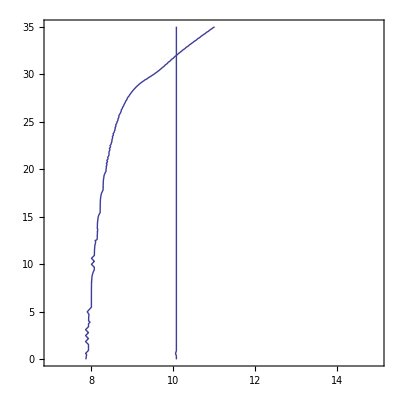

```mathematica
p1=ContourPlot[0==eq1diff[10^x,10^y],{x,7,15},{y,0,35}];
p2=ContourPlot[0==eq2diff[10^x,10^y],{x,7,15},{y,0,35}];
Show[{p1,p2}]
```

```mathematica
p2[[1,1,1]]
```

{7.86463,0.}

```mathematica
Dimensions[p2[[1,1]]][[1]]
```

299

```mathematica
SquaredEuclideanDistance[{0,0},{1,1}]
```

2

```mathematica
Sqrt[SquaredEuclideanDistance[p1[[1,1,1]],p2[[1,1,1]]]]
```

35.07

```mathematica
normmatrix=Table[Sqrt[SquaredEuclideanDistance[p1[[1,1,ii]],p2[[1,1,jj]]]],{ii,1,Dimensions[p1[[1,1]]][[1]]},{jj,1,Dimensions[p2[[1,1]]][[1]]}];
```

```mathematica
minelement[p1_,p2_]:=Module[{ii,jj,dist,dist0,whichii,whichjj,avgpoint},
dist0=10^(30);
For[ii=1,ii≤Dimensions[p1[[1,1]]][[1]],
For[jj=1,jj<=Dimensions[p2[[1,1]]][[1]],
dist=Sqrt[SquaredEuclideanDistance[p1[[1,1,ii]],p2[[1,1,jj]]]];
If[dist<dist0,dist0=dist;whichii=ii;whichjj=jj;];
(*Print["dist=",dist," jj=",jj," ii=",ii];*)
jj++;
];
ii++;
];
(* return *)
avgpoint={0.5*(p1[[1,1,whichii]][[1]]+p2[[1,1,whichjj]][[1]]),0.5*(p1[[1,1,whichii]][[2]]+p2[[1,1,whichjj]][[2]])};
{dist,whichii,whichjj,p1[[1,1,whichii]],p2[[1,1,whichjj]],avgpoint}
];
```

```mathematica
pickpoint=minelement[p1,p2][[6]]
```

{10.0626,31.875}

```mathematica
sols=FindRoot[{eq1diff[10^x,10^y]==0,eq2diff[10^x,10^y]==0},{x,pickpoint[[1]]},{y,pickpoint[[2]]}]
myT=10^sols[[1,2]];
mynpairssol=10^sols[[2,2]];
eqtotdiff[myT,mynpairssol]
```

{x→10.0826,y→31.9934}

2.18732×10^-16

```mathematica
Dimensions[p1[[1,1]]]
```

{183,2}

```mathematica
Min[normmatrix]
```

0.033973

```mathematica
sol={10.06,31.84}
sol=FindRoot[{eq1diff[10^x,10^y]==0,eq2diff[10^x,10^y]==0},{x,10.06},{y,31.84}]
```

{10.06,31.84}

{x→10.0826,y→31.9934}

```mathematica
sol[[1,2]]
```

10.0826

```mathematica
eqtotdiff[10^sol[[1,2]],10^sol[[2,2]]]
```

2.18732×10^-16

```mathematica
npairs0[rhobrad,10^10,bgaussrad]
```

4.8966571992148443289016515597×10^31

```mathematica
ne[rhobvalue]
```

1.9488727819368070410881069121×10^25

25.2897834902689269500492222493

10.2897834902689269500492222493

40.2897834902689269500492222493

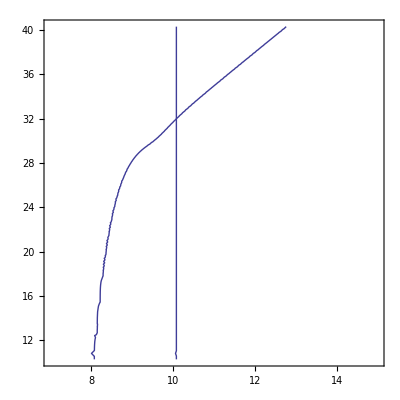

```mathematica
yavg=Log[10,ne[rhobvalue]]
ylow=yavg-15
yhigh=yavg+15
ylow=If[ylow<0,0,ylow];
p1=ContourPlot[0==eq1diff[10^x,10^y],{x,7,15},{y,ylow,yhigh}];
p2=ContourPlot[0==eq2diff[10^x,10^y],{x,7,15},{y,ylow,yhigh}];
Show[{p1,p2}]
```

```mathematica
pickpoint=minelement[p1,p2][[6]]
solstrial=FindRoot[{eq1diff[10^x,10^y]==0,eq2diff[10^x,10^y]==0},{x,pickpoint[[1]]},{y,pickpoint[[2]]}];
myT=10^(solstrial[[1,2]])
mynpairssol=10^(solstrial[[2,2]])
errorTnpairs=Abs[eqtotdiff[myT,mynpairssol]]
```

{10.0777,31.9626}

1.20935×10^10

9.84843×10^31

2.18732×10^-16